# Warming-induced changes to body size stabilize consumer-resource dynamics

## Matthew M Osmond, Matthew A Barbour, Joey R Bernhardt, Matthew W Pennell, Jennifer M Sunday, Mary I O’Connor Biodiversity Research Centre and Department of Zoology, University of British Columbia, Canada

Made with Mathematica 9

## Preliminaries

Plot settings

```mathematica
LabelSize=35; (*size of axis label text*)
FigureSize=650;  (*size of figure*)
TickSize=20;  (*size of tick text*)
Pad={{90,25},{70,10}};  (*whitespace to leave around figures, {{left,right},{bottom,top}}*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
LetterSize=20;  (*size of text in stability plots*)
```

Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*set current directory to be location of this file*)
imagedir="IMAGES/";(*directory to save figures in; make this directory before running*)
```

## The underlying consumer-resource dynamics

Equations 1 and 2 from Gilbert et al 2014 (with potential temperature dependencies added)

```mathematica
dRdt[R_,C_,T_]:=r[T] R(1-R/K[T])-f[R,T] R C;
dCdt[R_,C_,T_]:=e[T] f[R,T]R C-m[C,T]C;
```

where R is biomass of resource, C is biomass of consumer, T is temperature, K is resource carrying capacity, f R is the functional response, e is the conversion efficiency of resources into new consumers, and m is consumer mortality.

BCR at a given T, as defined by Gilbert (Eqn 5),

```mathematica
BCR[T_]:=(e[T] a[T]K[T])/m[T]
```

Equilibrium biomasses at given temperature assuming a type I functional response and density-independent consumer mortality (as in most of Gilbert)

```mathematica
Eq[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR[T_]:=C/R/.Eq[T][[3]]
```

The Jacobian evaluated at equilibrium (linear stability analysis)

```mathematica
Jac={{D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]}}/.Eq[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda=Eigenvalues[Jac];
```

## Re-creating Gilbert et al.’s Figure 3

Using equation for K in Table 1 of Gilbert. Want K = 100 at 15C (as in Figure 3 of Gilbert), so we need rate-constant K0 to be

```mathematica
K15=Solve[100==K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T/.T->273.15+15,K0];
```

Reproducing Figure 3A of Gilbert (same shape but numbers too large; can’t tell why from their figure legend)

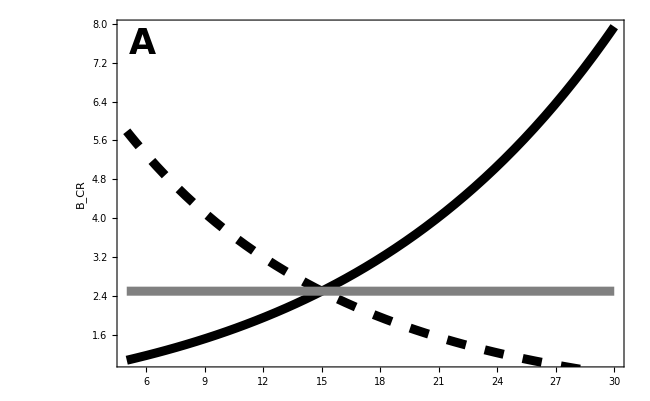

```mathematica
Show[
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thickness[0.01]}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"BCRGilbert.pdf",%];*)
```

Figure 3b of Gilbert (off by factor of ~3, again not sure why)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

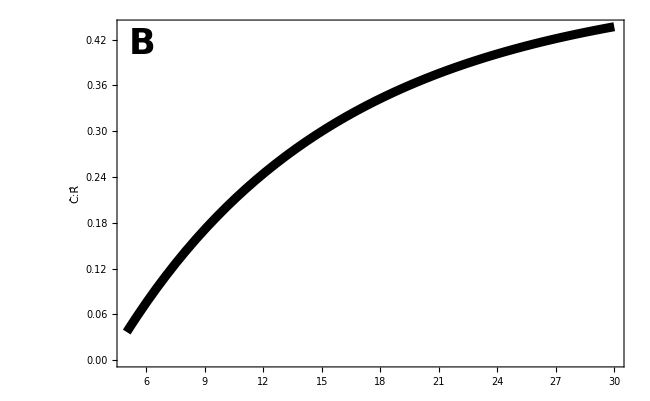

```mathematica
Show[Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thickness[0.01]}],
(*Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"CtoRGilbert.pdf",%];*)
```

Figure 3c of Gilbert

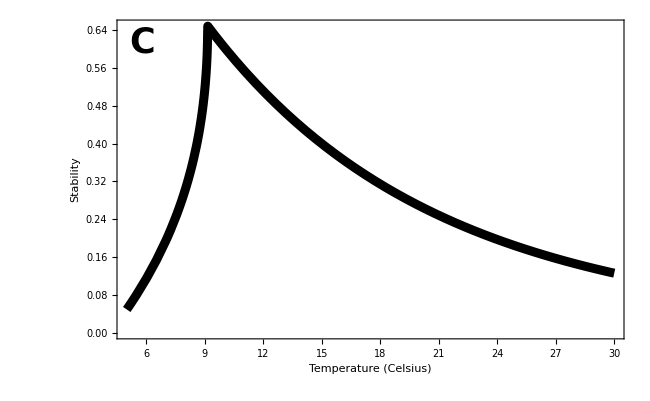

```mathematica
Show[Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Black,Thickness[0.01]}],
(*Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32]],{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"StabilityGilbert.pdf",%];*)
```

## Allowing all temperature dependencies

Here we add all the temperature dependencies, according to Table 1 of Gilbert et al.

```mathematica
cr={C,R};
GilbertTable1={
r[T]->r[M] Exp[-EB/(k T[R])],
K[T]->K[M] Exp[EB/(k T[R])-ES/(k T[S])],
m[T]->m[M] Exp[-Em/(k T[C])],
a[T]->a[M] Sqrt[Sum[(ν0[cr[[i]]] Exp[-Eν[cr[[i]]]/(k T[cr[[i]]])])^2,{i,1,Length[cr]}]],
e[T]->e[M]
};
```

To have the same population dynamics parameter values at 15 degrees as we did above with temperature dependence only in K, we need

```mathematica
aM15=Solve[0.1==a[T]/.GilbertTable1/.T[i_]->273.15+15,a[M]]//Flatten
```

{a[M]→0.1/(√(ⅇ^(-(0.00694083 Eν[C])/k) ν0[C]^2+ⅇ^(-(0.00694083 Eν[R])/k) ν0[R]^2))}

```mathematica
eM15=Solve[0.15==e[T]/.GilbertTable1/.T[i_]->273.15+15,e[M]]//Flatten
```

{e[M]→0.15}

```mathematica
KM15=Solve[100==K[T]/.GilbertTable1/.T[i_]->273.15+15,K[M]]//Flatten
```

{K[M]→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k)}

```mathematica
rM15=Solve[2==r[T]/.GilbertTable1/.T[i_]->273.15+15,r[M]]//Flatten
```

{r[M]→2. ⅇ^((0.00347041 EB)/k)}

```mathematica
mM15=Solve[0.6==m[T]/.GilbertTable1/.T[i_]->273.15+15,m[M]]//Flatten
```

{m[M]→0.6 ⅇ^((0.00347041 Em)/k)}

Now, BCR as a function of temperature is

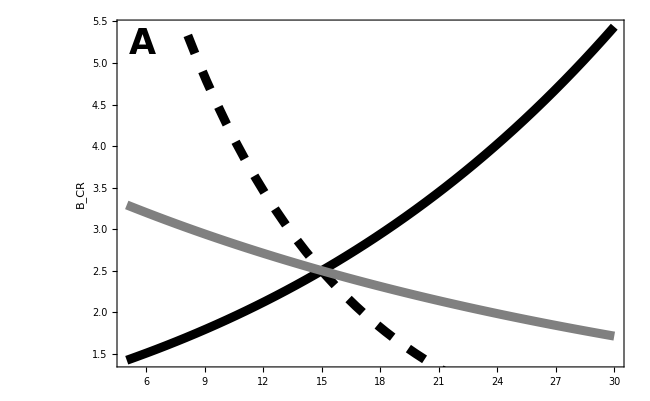

```mathematica
Show[
Plot[BCR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[BCR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"BCRAllTempDep.pdf",%];*)
```

This is the same qualitative result as Gilbert et al Figure 3A, with the gray curve now with a slightly non-zero slope (because, although K doesn’t vary with T, other parameters now do).

The biomass ratio is

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

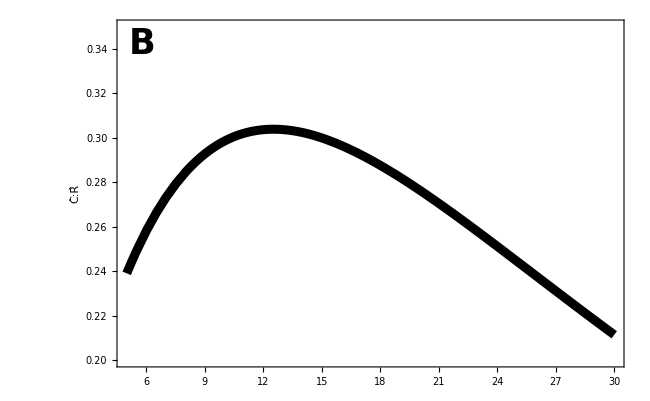

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]},Axes->False],
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],*)
PlotRange->{{5,30},{0.2,0.35}},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"CtoRAllTempDep.pdf",%];*)
```

The ratio now decreases at high temperatures (as opposed to the increase in Gilbert et al Figure 3B).

And stability:

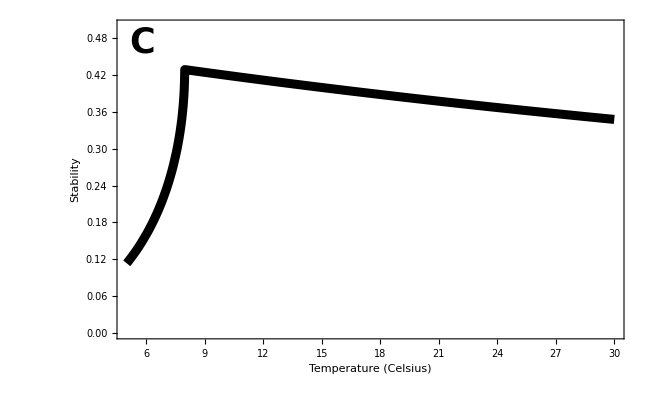

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
(*Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]},Axes->False,PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],*)
PlotRange->{0,0.5},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"StabilityAllTempDep.pdf",%];*)
```

With all the dependencies, stability still decreases with temperature, albeit slower than when only K depended on temperature (Gilbert Figure 3c).

The decrease in consumer:resource biomass at high temperatures, relative to Gilbert et al Figure 3B, is largely driven by the temperature dependence of consumer mortality (here we drop that dependence and see consumer:resource biomass increase with temperature, as it did before):

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

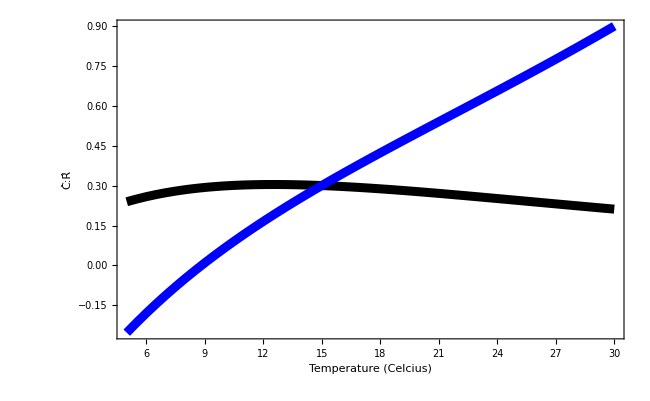

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celcius)",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None
]
```

The increase in stability at high temperatures, relative to Gilbert et al Figure 3C, is largely driven by the temperature dependence of consumer mortality (here we drop that dependence and see stability decline, as it did in Gilbert):

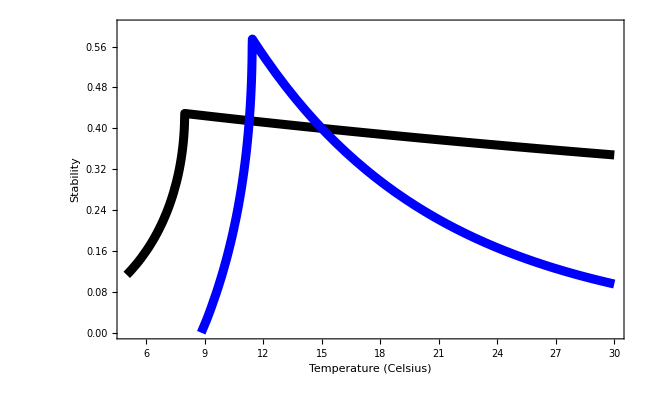

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None
]
```

## Adding mass-dependence and the temperature-size rule

Now we add dependence on body mass using the relations given in Table 1 of DeLong et al. 2015:

```mathematica
DeLongTable1={
r[M]->r0 M[R]^ρ,
K[M]->K0 M[R]^κ,
a[M]->a0 M[C]^α,
e[M]->e0 M[C]^ϵ,
m[M]->m0 M[C]^μ
};
```

We also want to add the temperature-size rule (TSR). From Forster et al. 2012 Figure 2 this is, for smaller organisms (where the TSR is linear):

```mathematica
TSR=M[i_]->M15[i](1-β[i](T[i]-(273.15+15)));
```

where M15[i], i={R,C}, is the mass of the resource or consumer at 15 degrees Celsius, β[i] is the percent decline in body size with a degree increase in temperature, and T[i] is the current temperature (in Kelvins).

To have the same population dynamics parameter values at 15C as in Gilbert et al 2014 Figure 3 we need

```mathematica
a15=Solve[0.1==a[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 M15[C]^(-1. α))/(√(ⅇ^(-(0.00694083 Eν[C])/k) ν0[C]^2+ⅇ^(-(0.00694083 Eν[R])/k) ν0[R]^2))}

```mathematica
e15=Solve[0.15==e[M]/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

### Effects on each parameter

Lets see how each parameter changes with temperature, with (red) and without (black) the TSR.

Attack rate: the TSR reduces the response to temperature

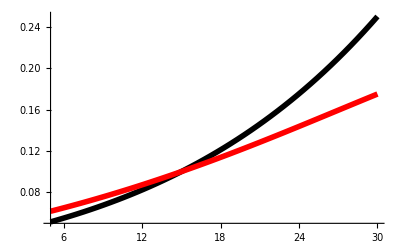

```mathematica
Show[
Plot[a[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[a[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}]
]
```

Resource intrinsic growth rate: the TSR increases the response to temperature

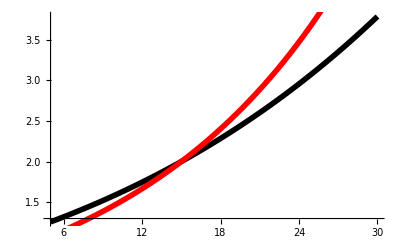

```mathematica
Show[
Plot[r[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[r[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}]
]
```

Resource carrying capacity: the TSR increases the response to temperature

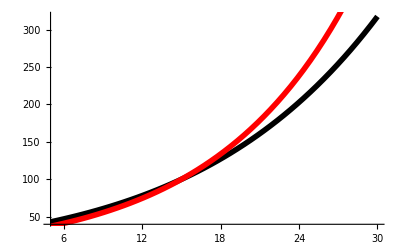

```mathematica
Show[
Plot[K[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[K[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}]
]
```

Consumer mortality rate: the TSR increases the response to temperature

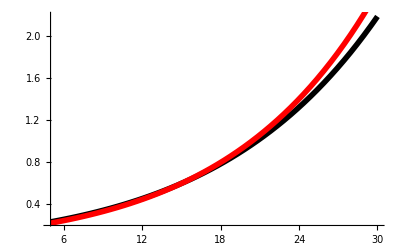

```mathematica
Show[
Plot[m[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[m[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}]
]
```

Note that for all temperature dependent parameters, the TSR increases the sensitivity to temperature in all except attack rate. In other words, the indirect effect of temperature on the parameters, through body mass, acts in the same direction as the direct effect of temperature on the parameters, except in the case of attack rate, where direct and indirect effects oppose one another and reduce the sensitivity of attack rate to temperature.

### Numerical solutions of temporal dynamics

Stability conditions for coexistence equilibrium (for stable node or focus need trace negative and determinant positive):

```mathematica
FullSimplify[Tr[Jac],{a[T]>0,e[T]>0,K[T]>0,m[T]>0,r[T]>0}]
```

-(m[T] r[T])/(a[T] e[T] K[T])

So the trace is always negative, meaning we can’t have an unstable node or focus. But we could have a saddle if the determinant can be negative:

```mathematica
FullSimplify[Det[Jac],{a[T]>0,e[T]>0,K[T]>0,m[T]>0,r[T]>0}]
```

m[T] (1-m[T]/(a[T] e[T] K[T])) r[T]

which is can be if a e K < m.

Simplified dynamics (saddle)

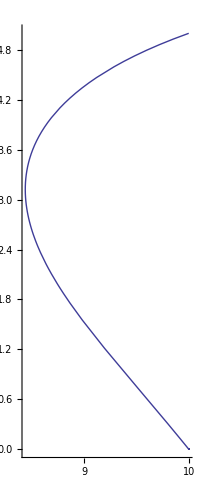

```mathematica
deqns={
dRdt[R,C,T],
dCdt[R,C,T]
}/.f[R,T]->a[T]/.m[C,T]->m[T]/.R->R[t]/.C->CO[t]/.a[T]->0.1/.e[T]->0.15/.K[T]->10/.r[T]->2/.m[T]->0.6;

dsol=NDSolve[{
D[R[t],t]==deqns[[1]],
D[CO[t],t]==deqns[[2]],
R[0]==10,
CO[0]==5
},
{R,CO},
{t,0,100}
];

ParametricPlot[Evaluate[{R[t],CO[t]}/.dsol],{t,0,100},PlotRange->{{0,All},{0,All}}]
```

Simplified dynamics (stable)

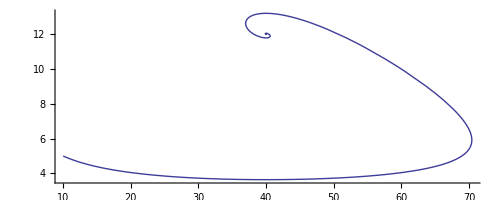

```mathematica
deqns={
dRdt[R,C,T],
dCdt[R,C,T]
}/.f[R,T]->a[T]/.m[C,T]->m[T]/.R->R[t]/.C->CO[t]/.a[T]->0.1/.e[T]->0.15/.K[T]->100/.r[T]->2/.m[T]->0.6;

dsol=NDSolve[{
D[R[t],t]==deqns[[1]],
D[CO[t],t]==deqns[[2]],
R[0]==10,
CO[0]==5
},
{R,CO},
{t,0,100}
];

ParametricPlot[Evaluate[{R[t],CO[t]}/.dsol],{t,0,100},PlotRange->{{0,All},{0,All}}]
```

The dynamics, with (black) and without (gray) the TSR

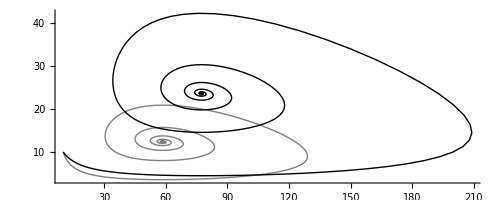

```mathematica
R0=10;
C0=10;
tmax=100;
T=30;

deqnsNoTSR={
dRdt[R,C,T],
dCdt[R,C,T]
}/.f[R,T]->a[T]/.m[C,T]->m[T]/.R->R[t]/.C->CC[t]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15;

dsolNoTSR=NDSolve[{
D[R[t],t]==deqnsNoTSR[[1]],
D[CC[t],t]==deqnsNoTSR[[2]],
R[0]==R0,
CC[0]==C0
},
{R,CC},
{t,0,tmax}
];

deqnsWithTSR={
dRdt[R,C,T],
dCdt[R,C,T]
}/.f[R,T]->a[T]/.m[C,T]->m[T]/.R->R[t]/.C->CC[t]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15;

dsolWithTSR=NDSolve[{
D[R[t],t]==deqnsWithTSR[[1]],
D[CC[t],t]==deqnsWithTSR[[2]],
R[0]==R0,
CC[0]==C0
},
{R,CC},
{t,0,tmax}
];

Show[
ParametricPlot[Evaluate[{R[t],CC[t]}/.dsolNoTSR],{t,0,tmax},PlotRange->{{0,All},{0,All}},PlotStyle->Gray],
ParametricPlot[Evaluate[{R[t],CC[t]}/.dsolWithTSR],{t,0,tmax},PlotRange->{{0,All},{0,All}},PlotStyle->Black]
]

Clear[R0,C0,tmax,T,deqnsNoTSR,dsolNoTSR,deqnsWithTSR,dsolWithTSR]
```

## BCR, C:R, and stability with and without the TSR

Now, with the TSR the BCR as a function of temperature is

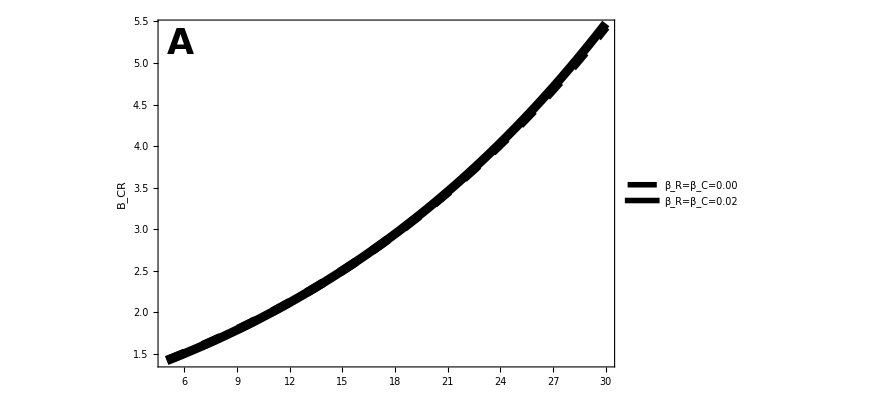

```mathematica
Legended[
Show[
(*Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[
BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
],
Placed[
LineLegend[{
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.25]]
},
{
Style["β_R=β_C=0.00",LabelSize],
Style["β_R=β_C=0.02",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.25,0.6}
] 
]

(*Export[imagedir<>"BCRAllTempMassDep.pdf",%];*)
```

As the curves overlap almost perfectly, the added mass dependence and TSR do not affect the response of BCR to temperature.

Biomass ratios:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

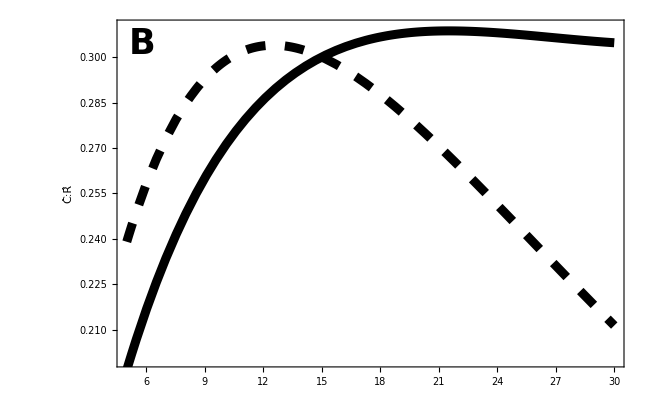

```mathematica
Show[
(*Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False],*)
PlotRange->{0.2,0.31},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"CtoRAllTempMassDep.pdf",%];*)
```

Here we see that when we add the TSR the ratio no longer decreases over reasonable temperatures. I.e., temperature directly decreases consumer:resource biomass (through its affect on cosumer mortality; see previous section), but it also decreases body sizes, and decreased body size increases consumer:resource biomass (by increasing conversion efficiency and intrinsic growth rate; see below). In other words, the direct and indirect effects of temperature are opposing.

Stability:

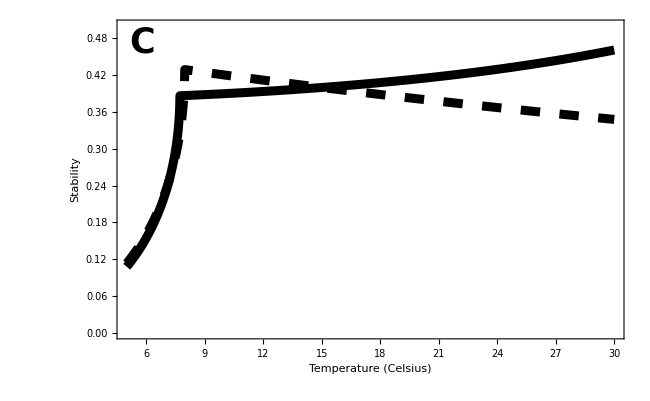

```mathematica
Show[(*Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
(*Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},PlotRange->{0,All}],*)
PlotRange->{0,0.5},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"StabilityAllTempMassDep.pdf",%];*)
```

With the temperature-size rule, stability increases with increasing temperature (as opposed to the decrease without the TSR). Again, temperature directly destabilizes, but indirectly, through its effect on body size (which decreases attack rate and increases intrinsic growth rate), increasing temperature stabilizes the dynamics.

The lack of decrease in C:R at high temperatures, relative to the case without the TSR, is driven by the indirect effect of temperature on conversion efficiency (purple; increases with decreasing body size and hence with temperature) and resource intrinsic growth rate (blue; increases with decreasing body size and hence with temperature. When we drop these effects the curve goes back to the without TSR case:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

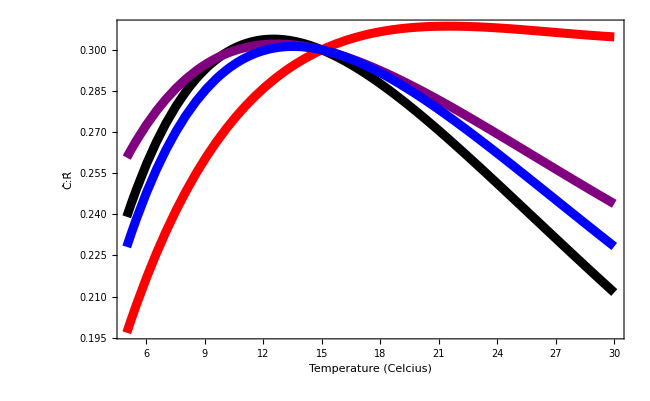

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->0/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Purple,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->0/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celcius)",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]
```

The increase in stability at high temperatures, relative to the case without the TSR, is driven by the indirect effect of temperature on attack rate (which decreases with decreasing body size) and resource intrinsic growth rate (which increases with increasing body size). When we drop these effects the response looks similar to the response without the TSR:

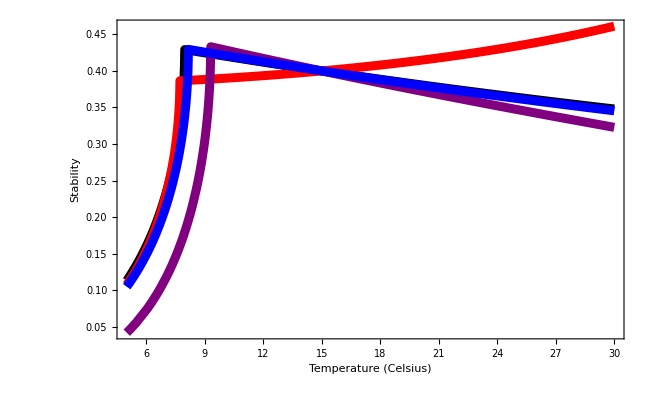

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->0/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Purple,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->0/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["",LabelSize,Bold],Scaled@letpos]
}
]
```

Note that when things are already not stable (saddle node created by lowering K, meaning there aren’t enough resources to support consumer), then the TSR causes further instability.

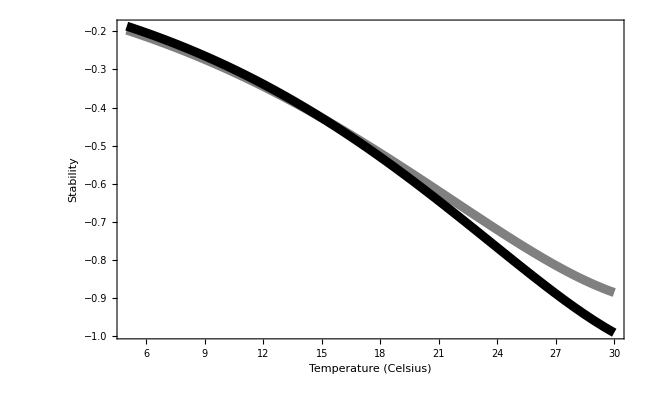

```mathematica
k15Saddle=Solve[10==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten;

Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15Saddle/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->All],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15Saddle/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["",LabelSize,Bold],Scaled@letpos]
}
]
```

## Parameter perturbation [r(T_ref) = 0.2, K(T_ref) = 1000]

```mathematica
r15b=Solve[0.2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→0.2 ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
k15b=Solve[1000==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→1000. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

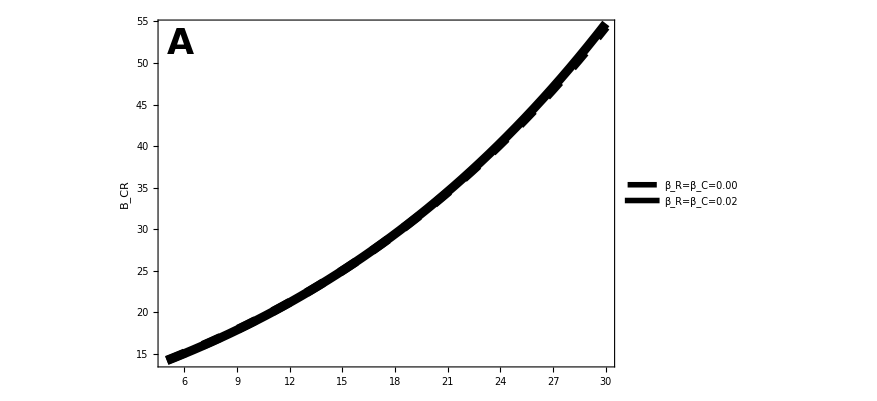

```mathematica
Legended[
Show[
(*Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[
BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15b/.r15b/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15b/.r15b/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
],
Placed[
LineLegend[{
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.25]]
},
{
Style["β_R=β_C=0.00",LabelSize],
Style["β_R=β_C=0.02",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.25,0.6}
] 
]

(*Export[imagedir<>"BCRAllTempMassDep.pdf",%];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

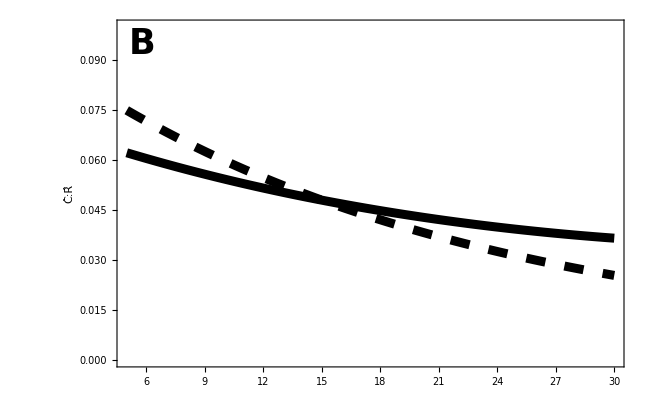

```mathematica
Show[
(*Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15b/.r15b/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15b/.r15b/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False],*)
PlotRange->{0,0.1},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"CtoRAllTempMassDep.pdf",%];*)
```

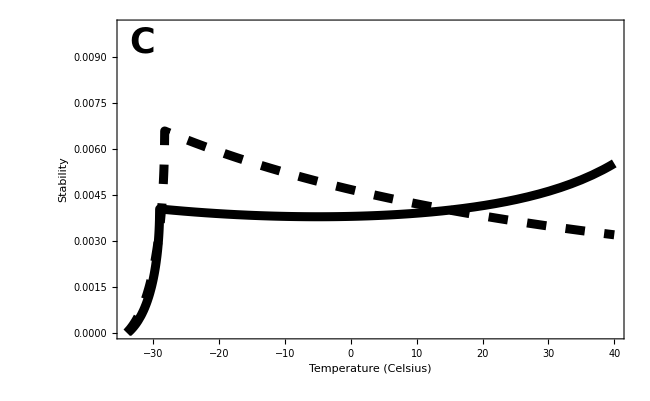

```mathematica
Show[(*Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15b/.r15b/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,-40,40},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15b/.r15b/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,-40,40},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
(*Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},PlotRange->{0,All}],*)
PlotRange->{0,0.01},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"StabilityAllTempMassDep.pdf",%];*)
```

## Varying strengths of the temperature-size rule

BCR:

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[R]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[R]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[R]] - 0} must be a list of equalities or real-valued functions.

General::stop: Further output of Plot :: exclul will be suppressed during this calculation.

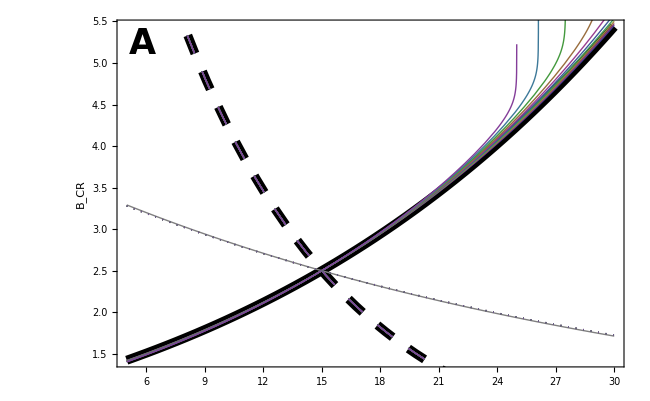

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[Evaluate@Table[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->β/.T[i_]->T+273.15,{β,0.01,0.1,0.01}],{T,5,30},PlotStyle->{Thick}],
Plot[Evaluate@Table[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{β,0.01,0.1,0.01}],{T,5,30},PlotStyle->{Dashing[Large]}],Plot[Evaluate@Table[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{β,0.01,0.1,0.01}],{T,5,30},PlotStyle->{Dotted}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]
```

Biomass ratios:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[C]] - 0, Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[R]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[C]] - 0, Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[R]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[C]] - 0, Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[C]] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[R]] - 0} must be a list of equalities or real-valued functions.

General::stop: Further output of Plot :: exclul will be suppressed during this calculation.

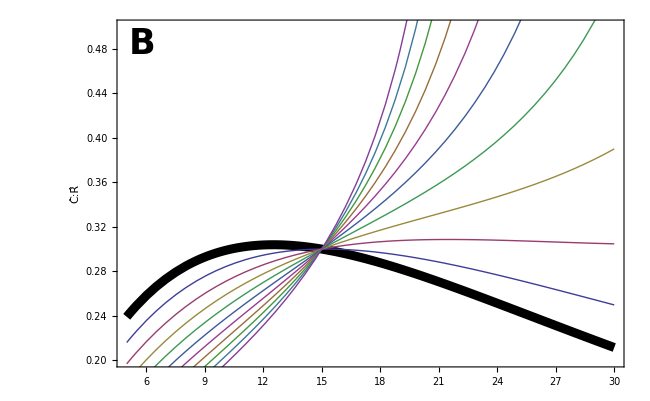

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],Plot[  Evaluate@Table[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->β/.T[i_]->T+273.15,{β,0.01,0.1,0.01}],{T,5,30},PlotStyle->Thick,Axes->False],
PlotRange->{0.2,0.5},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]
```

Stability:

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.01\ (-15. + T))\ M15[C]] - 0, « 25 », (3.01934×10^-9\ Re[ⅇ^Plus[« 2 »]\ M15[« 1 »]^0.5\ Times[« 2 »]^0.81\ (Times[« 6 »] + Times[« 2 »])/√Power[« 2 »]\ Times[« 2 »]^0.5\ M15[« 1 »]^0.81] - 3.01934×10^-9\ Re[ⅇ^Plus[« 2 »]\ M15[« 1 »]^0.5\ Times[« 2 »]^0.81\ (Times[« 6 »] + Power[« 2 »])/√Power[« 2 »]\ Times[« 2 »]^0.5\ M15[« 1 »]^0.81]) - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.02\ (-15. + T))\ M15[C]] - 0, « 25 », (3.01934×10^-9\ Re[ⅇ^Plus[« 2 »]\ M15[« 1 »]^0.5\ Times[« 2 »]^0.81\ (Times[« 6 »] + Times[« 2 »])/√Power[« 2 »]\ Times[« 2 »]^0.5\ M15[« 1 »]^0.81] - 3.01934×10^-9\ Re[ⅇ^Plus[« 2 »]\ M15[« 1 »]^0.5\ Times[« 2 »]^0.81\ (Times[« 6 »] + Power[« 2 »])/√Power[« 2 »]\ Times[« 2 »]^0.5\ M15[« 1 »]^0.81]) - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Im[ⅇ^-10672.9/273.15  + T] - 0, Im[(1 - 0.03\ (-15. + T))\ M15[C]] - 0, « 25 », (3.01934×10^-9\ Re[ⅇ^Plus[« 2 »]\ M15[« 1 »]^0.5\ Times[« 2 »]^0.81\ (Times[« 6 »] + Times[« 2 »])/√Power[« 2 »]\ Times[« 2 »]^0.5\ M15[« 1 »]^0.81] - 3.01934×10^-9\ Re[ⅇ^Plus[« 2 »]\ M15[« 1 »]^0.5\ Times[« 2 »]^0.81\ (Times[« 6 »] + Power[« 2 »])/√Power[« 2 »]\ Times[« 2 »]^0.5\ M15[« 1 »]^0.81]) - 0} must be a list of equalities or real-valued functions.

General::stop: Further output of Plot :: exclul will be suppressed during this calculation.

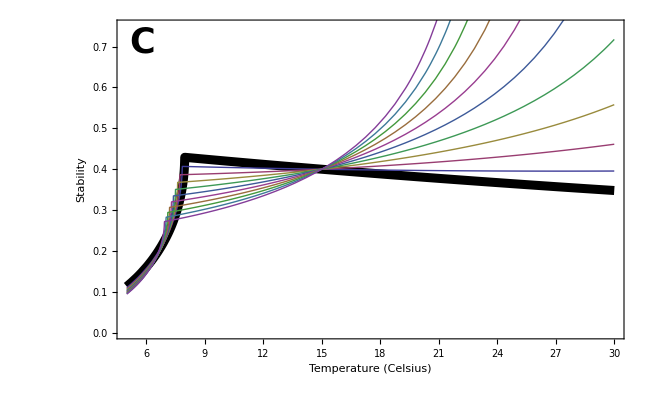

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[Evaluate@Table[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->β/.T[i_]->T+273.15]],{β,0.01,0.1,0.01}],{T,5,30},PlotStyle->{Thick},PlotRange->{0,All}],
PlotRange->{0,0.75},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]
```

So TSRs greater than 1% cause observable (here) differences from predictions not incorporating the TSR. 
TSRs greater than roughly 2% cause qualitative differences, with greater TSRs leading to even larger qualitative differences.

## Exploring asymmetric temperature-size responses (resource < consumer)

In the previous section we’ve supposed that the consumer and resource have the same TSR response. Lets relax that. If the consumer is larger than the resource then, according to Forster et al 2012 Figure 2, it might also have a larger TSR response, say maybe a 4% decrease with degree, rather than the 2% for unicells (we are keeping the assumption that the loss is linear).

With a 4% TSR in consumer and a 2% TSR in resource, our predictions become:

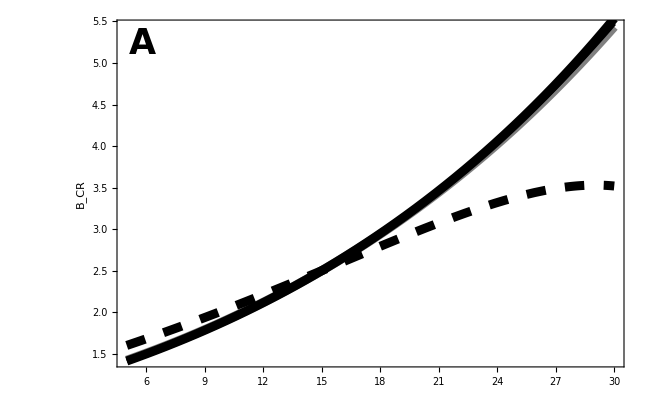

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.005],Black}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Blue,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Lighter[Blue]}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"BCRAllTempMassDepAsymm.pdf",%];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

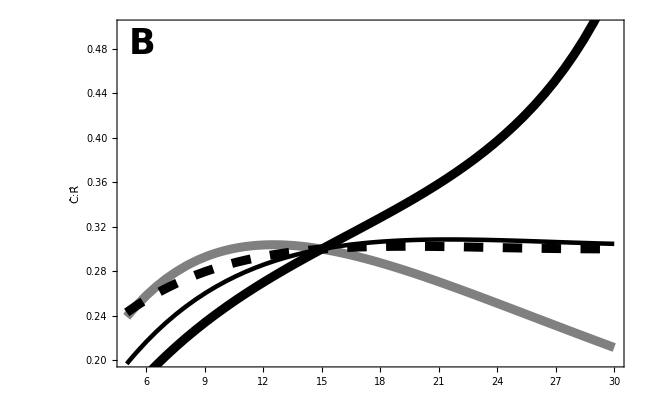

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
PlotRange->{0.2,0.5},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"CtoRAllTempMassDepAsymm.pdf",%];*)
```

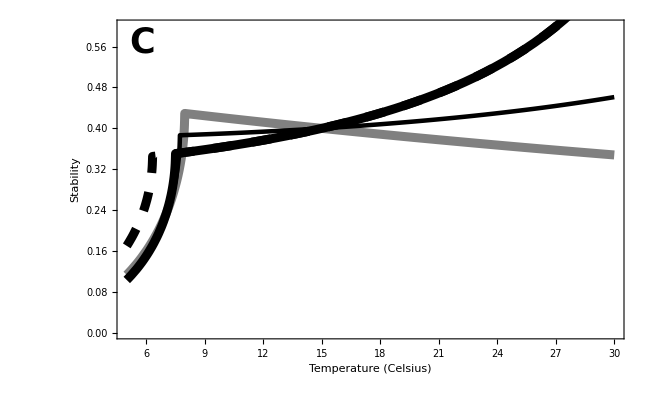

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"StabilityAllTempMassDepAsymm.pdf",%];*)
```

## Exploring asymmetric temperature-size responses (resource > consumer)

If the asymmetry goes the other way we might see different results. With a 4% TSR in resource and a 2% TSR in consumer, our predictions become:

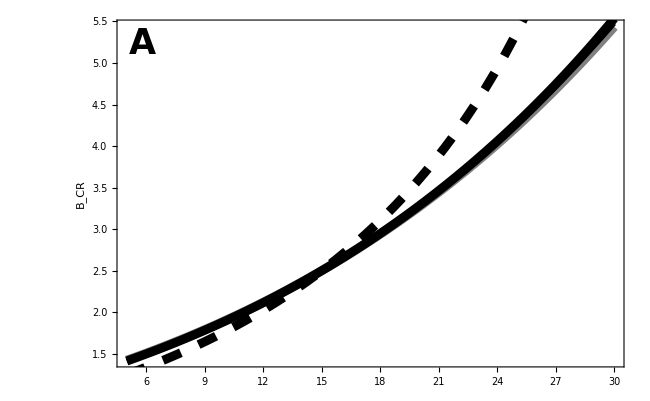

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.005],Black}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Blue,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Lighter[Blue]}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"BCRAllTempMassDepAsymm.pdf",%];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

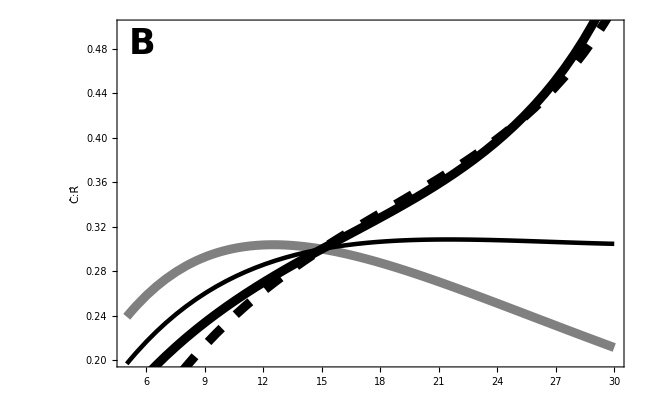

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
PlotRange->{0.2,0.5},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"CtoRAllTempMassDepAsymm.pdf",%];*)
```

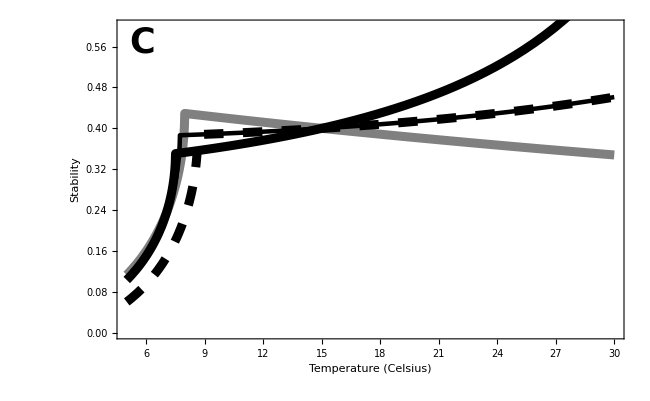

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"StabilityAllTempMassDepAsymm.pdf",%];*)
```

## Type-II functional response

BCR at a given T, like that defined by Gilbert et al (Eqn 5), but with type-ll functional response

```mathematica
BCR2[T_]:=(e[T] f[R,T]K[T])/m[C,T] /.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T]
```

Equilibrium biomasses at given temperature assuming a type Il functional response and density-independent consumer mortality

```mathematica
Eq2[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR2[T_]:=C/R/.Eq2[T][[3]]
```

The Jacobian evaluated at equilibrium (determines stability)

```mathematica
Jac2={{D[dRdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],C]}}/.Eq2[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda2=Eigenvalues[Jac2];
```

Now the dependencies. We can use the scalings of the other parameters from Gilbert and DeLong:

```mathematica
GilbertDeLongT={r[T]->ⅇ^(-EB/(k T[R])) r[M],K[T]->ⅇ^(EB/(k T[R])-ES/(k T[S])) K[M],m[T]->ⅇ^(-Em/(k T[C])) m[M],e[T]->e[M]};
GilbertDeLongM={r[M]->r0 M[R]^ρ,K[M]->K0 M[R]^κ,e[M]->e0 M[C]^ϵ,m[M]->m0 M[C]^μ};
```

The attack rate and handling time scalings are (in a 2D environment; Rall et al. 2012)

```mathematica
RallT={h[T]->ⅇ^(-Eh/(k T[C])) h[M],a[T]->ⅇ^(-Ea/(k T[C])) a[M]};
RallM={h[M]->h0 M[C]^hC M[R]^hR,a[M]->a0 M[C]^aC M[R]^aR};
```

To have the same population dynamics parameter values at 15C as in Gilbert et al. Figure 3, we need

```mathematica
ah15=Solve[0.1==Simplify[a[T]/(1+a[T]h[T]R)/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 ⅇ^((0.00347041 Ea)/k) M15[C]^(-1. aC) M15[R]^(-1. aR))/(1.-(1. 1.^(hC-1. ϵ+μ) ⅇ^(-(0.00347041 Eh)/k-(0.00347041 Em)/k) h0 m0 M15[C]^(hC-1. ϵ+μ) M15[R]^hR)/e0)}

```mathematica
e15=Solve[0.15==e[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

Changes in attack rate (solid) and capture rate (dashed) with temperature, with (black) and without (gray) the TSR

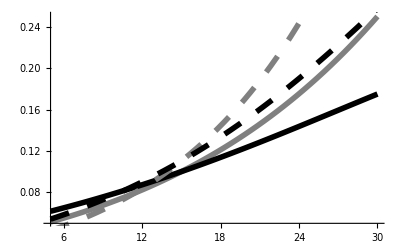

```mathematica
Show[Plot[a[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],
Plot[a[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[a[T]/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.0/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Thickness[0.01],Gray,Dashing[Large]}],
Plot[a[T]/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}]
]
```

Changes in handling time with temperature, with and without the TSR

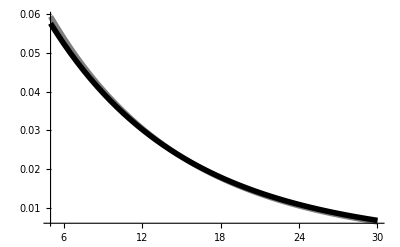

```mathematica
Show[
Plot[h[T]/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.0/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Thickness[0.01],Gray}],
Plot[h[T]/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Thickness[0.01],Black}]
]
```

BCR as a function of temperature

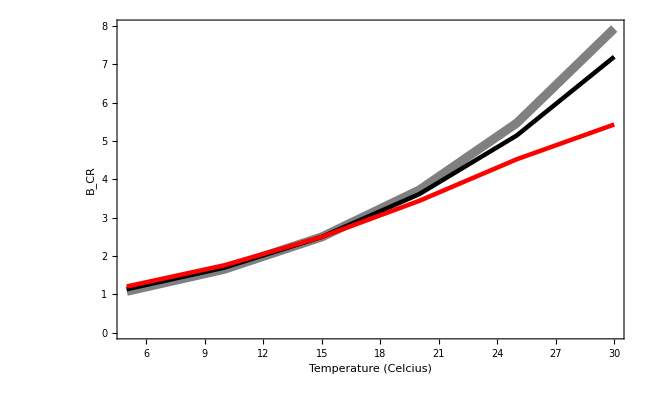

```mathematica
Show[
ListPlot[Table[{t,Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Gray,Thickness[0.01]},Axes->False, Joined->True],
ListPlot[Table[{t,Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Black,Thickness[0.005]},Axes->False, Joined->True],
ListPlot[Table[{t,Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.05/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Red,Thickness[0.005]},Axes->False, Joined->True],
PlotRange->{0,8},
Frame->True, 
FrameLabel->{Style["Temperature (Celcius)",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None
(*PlotRangeClipping->False,*)
]
```

and the TSR now lowers BCR slightly at high temperatures (it did not with type-I with both β=0.02).

C:R as a function of temperature

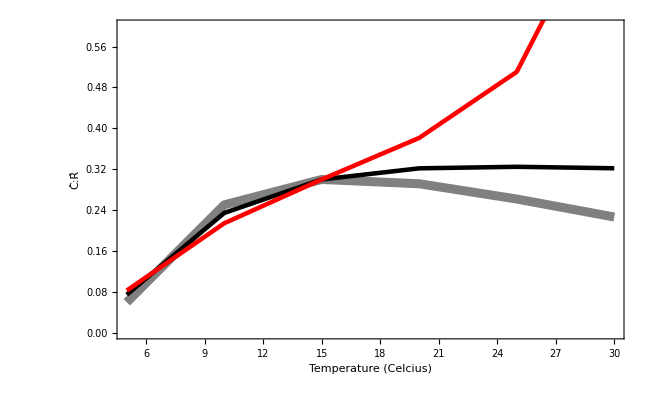

```mathematica
Show[
ListPlot[Table[{t,CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}, Joined->True],
ListPlot[Table[{t,CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}, Joined->True],
ListPlot[Table[{t,CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.05/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Red,Thickness[0.005]},PlotRange->{0,All}, Joined->True],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celcius)",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None
]
```

this is the same pattern we saw with the type-I.

Stability as a function of temperature

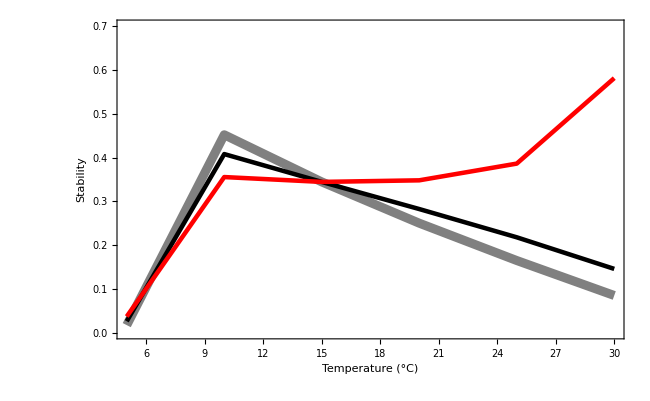

```mathematica
Show[ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Gray,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Black,Thickness[0.005]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.05/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Red,Thickness[0.005]},PlotRange->All, Joined->True],
PlotRange->{0,0.7},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRange->All
]
```

this is the same pattern we saw with the type-I (better stability with TSR at warm temps) but we now need a larger TSR to get increases in stability with temp (red).

### Handling time

Note that although we have to give values for handling time h0 and masses M15[i]s at 15 degreess in order to produce the above curves, the results do not depend on them - except in the case of stability, where h0 has a big effect.

The effect of h0 on stability with the type-II functional response:

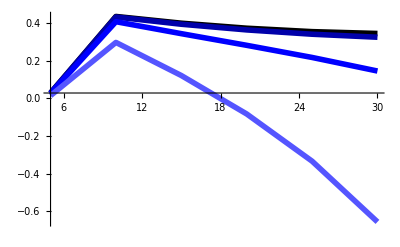

```mathematica
Show[
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->0/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Black,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-14/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Darker[Blue],Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Blue,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->5*10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Lighter[Blue],Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->{0,All}
]
```

ie, the greater the handling time the less stable things are, and the faster stability declines with higher temperatures.

Note that while handling time decreases faster with temperature when h0 is larger (this should stabilize things)

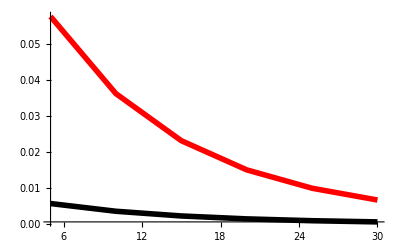

```mathematica
Show[
ListPlot[Table[{t,h[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-14/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Black,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,h[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Red,Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->{0,All}
]
```

...the functional responses change similarly with temperature (because R must be canceling out the effect of h0)

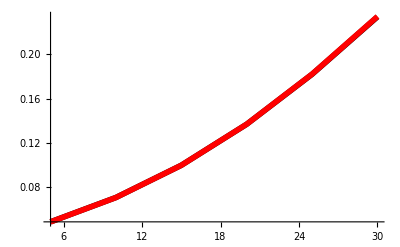

```mathematica
Show[
ListPlot[Table[{t,a[T]/(1+a[T]h[T]R)/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-14/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Black,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,a[T]/(1+a[T]h[T]R)/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Red,Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->All
]
```

The difference is in the derivative (which is important for stability - we take derivatives to get the Jacobian)

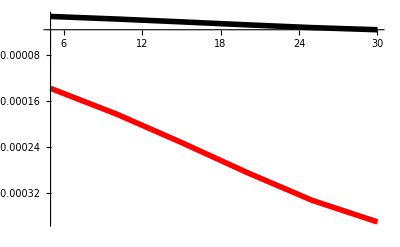

```mathematica
Show[
ListPlot[Table[{t,D[a[T]/(1+a[T]h[T]R),R]/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-14/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Black,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,D[a[T]/(1+a[T]h[T]R),R]/.Eq2[T][[3]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1},{t,5,30,5}],PlotStyle->{Red,Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->All
]
```

Here we see that the larger h0 means faster declines in the derivative of the functional response with respect to R as temperatures warm, meaning the system is more sensitive to perturbation.

When h0 is large enough to cause instability, the TSR causes instability to increase faster with temperature

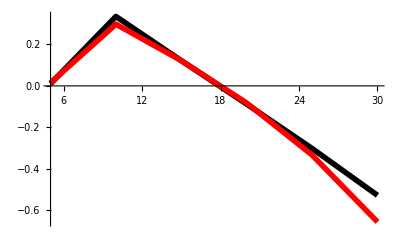

```mathematica
Show[
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.0/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->5*10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Black,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->5*10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Red,Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->All
]
```

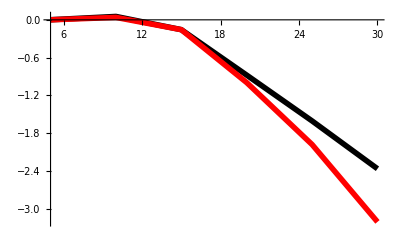

```mathematica
Show[
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.0/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-12/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Black,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-12/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Red,Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->All
]
```

## Type-II functional response continued: Improving Rall’s fit

Response of capture rate to temperature, with (blue) and without (black) the TSR:

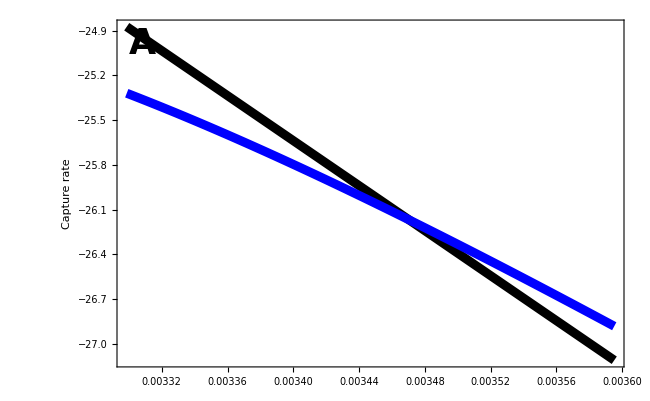

```mathematica
Show[
Plot[Log[a[T]/a0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[a[T]/a0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.β[i_]->0.02/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Capture rate",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"CaptureTSRSymm.pdf",%];*)
```

The TSR lowers the activation energy of capture rate, which goes in the same direction as the discrepancy seen in Rall (see Figure 3a in Rall et al 2012).

With an asymmetric TSR this reponse is even stronger			:

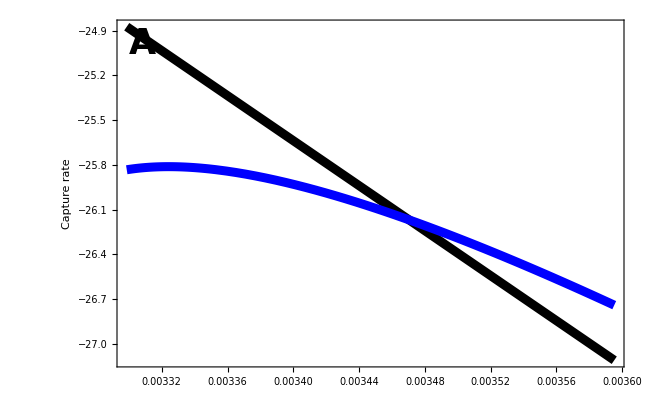

```mathematica
Show[
Plot[Log[a[T]/a0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[a[T]/a0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.β[R]->0.02/.β[C]->0.04/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Capture rate",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"CaptureTSRAsymm.pdf",%];*)
```

And for handling time:

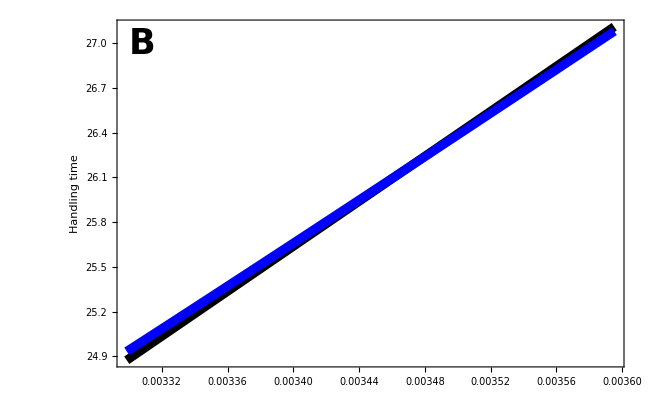

```mathematica
Show[
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[h[T]/h0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.β[i_]->0.02/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Handling time",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"HandlingTSRSymm.pdf",%];*)
```

Here the TSR (slightly) decreases the activation energy of handling time. But this is with same TSR in resource and consumer. If we allow the consumer to have a larger TSR, then we have

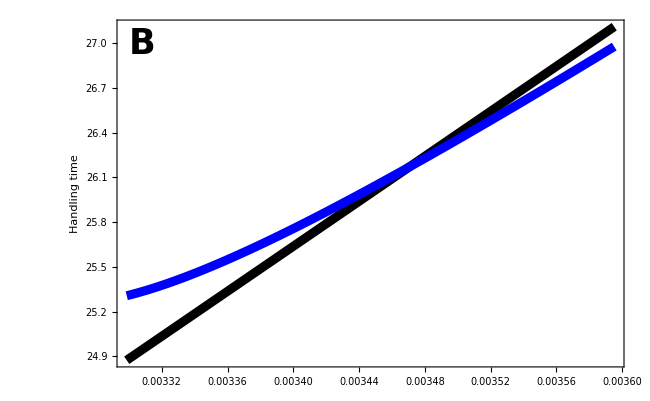

```mathematica
Show[
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[h[T]/h0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[R]->1/.M15[C]->1/.β[R]->0.02/.β[C]->0.04/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Handling time",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

(*Export[imagedir<>"HandlingTSRAsymm.pdf",%];*)
```

which makes the activation energy of handling time smaller, as in Rall (see Figure 3d).

## A functional response that depends on the body size ratio

### Summary

Functional responses tend to be roughly type-II when consumers and resources have similar body sizes, but become more sigmoidal when consumers are much bigger than their resource, as resources are then harder to find when rare Kalinkat et al (2013). To capture this shift Kalinkat et al (2013) use the generalized functional response $f(R)=\frac{b}{1 + bhR^{1+q}}$, where $q = q_{max} D^2 / (q_0^2 + D^2)$ depends on the body size ratio of consumer to resource, $D = M_C/M_R$. The scaling parameters $q_{max}$ and $q_0^2$ are the asymptotic value and half-saturation constant of $q$, respectively. The important thing to note is that when the consumer is much smaller than the resource ($D\approx0$) then $q \approx 0$ and the functional response is roughly type-II. As $D$ increases so does $q$, and when $q>0$ the functional response is type-III. Without a temperature-size response the body mass ratio remains constant with temperature and therefore the form of the functional response is not expected to change. However, with a temperature-size response that differs between resource and consumer, the ratio of body sizes will change and influence the form of the functional response. Because consumers are often larger than their resource, and because larger aquatic organisms are expected to have greater reductions in body size with temperature (Forster et al., 2012; Horne et al., 2015), the ratio of consumer to resource body size is expected to decrease with temperature. As stated above, lower consumer to resource body size ratios produce type-II functional responses ($\lim_{D\rightarrow0} q = 0$), which are less stable than type-III functional responses (McCann, 2011; Murdoch et al., 2003).  Hence, the temperature-size rule can be said to destabilize the consumer-resource dynamics at high temperatures by promoting type-II functional responses. However, the amount by which the shape of the functional response is adjusted by the temperature-size rule does not appear to be large and therefore the stabilizing effects discussed in previous sections will likely prevail (see Analyses section directly below for details).

### Analyses

This section is based on Kalinkat et al. 2013. who discuss how the functional response changes with the ratio of body size between consumer and resources.

In particular, we let the functional response be

```mathematica
g[R_,T_]:=(b[T] R^q[M])/(1+h[T]b[T] R^(1+q[M]))
```

such that when q=0 we have a type-2 functional response and when q>0 we have a type-3 (sigmoidal):

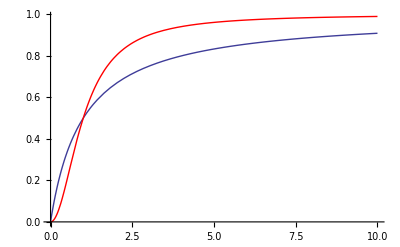

```mathematica
Show[
Plot[g[R,T]R/.b[T]->1/.h[T]->1/.q[M]->0,{R,0,10},PlotRange->{0,All}],
Plot[g[R,T]R/.b[T]->1/.h[T]->1/.q[M]->1,{R,0,10},PlotRange->{0,All},PlotStyle->Red],
PlotRange->{0,All}
]
```

We say q is a function of body  mass M, because it depends on the ratio of consumer to resource body size

```mathematica
q[M_]:=(qmax (M[C]/M[R])^2)/(q0^2+(M[C]/M[R])^2)
```

where qmax and q0 are scaling parameters that determine the shape of the sigmoidal response (qmax is the asymptote, q0^2 is the half-saturation constant):

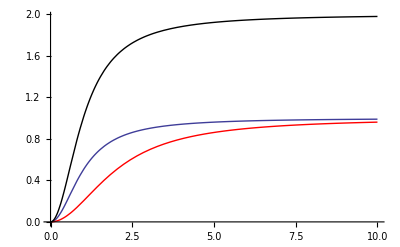

```mathematica
Show[
Plot[q[M]/.M[C]->a M[R]/.qmax->1/.q0->1,{a,0,10},PlotRange->{0,All}],
Plot[q[M]/.M[C]->a M[R]/.qmax->1/.q0->2,{a,0,10},PlotRange->{0,All},PlotStyle->Red],
Plot[q[M]/.M[C]->a M[R]/.qmax->2/.q0->1,{a,0,10},PlotRange->{0,All},PlotStyle->Black]
]
```

The fitted values in Kalinkat give the following curve

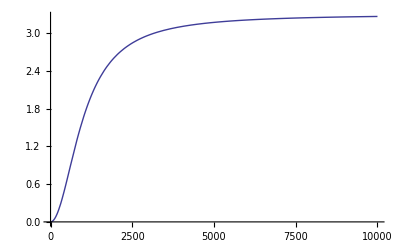

```mathematica
Plot[q[M]/.M[C]->a M[R]/.qmax->3.3/.q0->10^3,{a,0,10^4},PlotRange->{0,All},PlotStyle->Thick]
```

What effect does the TSR have on q?

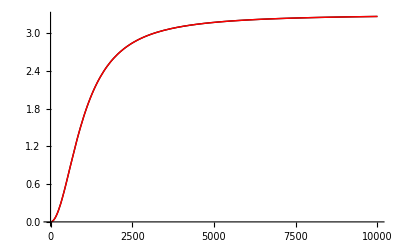

```mathematica
Show[
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0/.β[C]->0/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Black],
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0.02/.β[C]->0.02/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Red]
]
```

As we might expect, because q depends on the ratio of body sizes, if both resource and consumer have the same TSR, then the TSR has no affect on q.

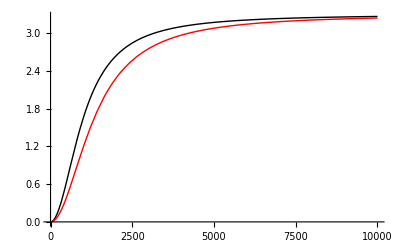

```mathematica
Show[
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0/.β[C]->0/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Black],
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0.02/.β[C]->0.04/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Red]
]
```

However, when the consumer has a larger TSR than the resource (4% vs 2%), the body mass ratio decreases with temperature, decreasing q and therefore slowing the switch from type-2 to type-3. Because type-3 is more stable, the TSR may be said to reduce stability by this mechanism (however, as we can see in the above plot, with the TSR (red) q is not reduced by much).

## Figure 1 (A,B,C) [ES>EB, type-I]

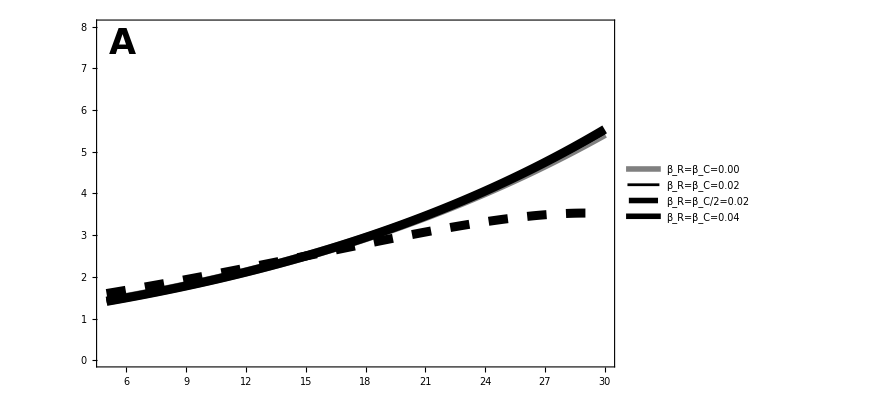

```mathematica
Legended[
Show[
(*Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[
BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray},Axes->False,PlotRangePadding->None],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.005],Black},PlotRangePadding->None],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]},PlotRangePadding->None],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black},PlotRangePadding->None],
PlotRange->{0,8},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"B_CR"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.25]],
Directive[Black,Thickness[0.1]],
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.35]]
},
{
Style["β_R=β_C=0.00",LabelSize],
Style["β_R=β_C=0.02",LabelSize],
Style["β_R=β_C/2=0.02",LabelSize],
Style["β_R=β_C=0.04",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.7}
] 
]

Export[imagedir<>"BCRType1.pdf",%];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

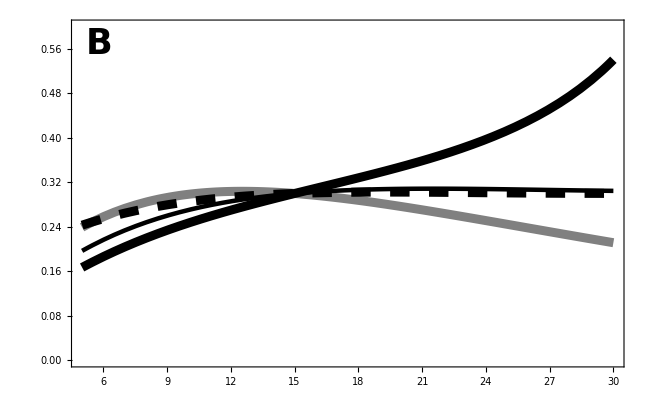

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"Ĉ:R̂"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Ĉ:R̂",LabelSize],Scaled@ylabpos],90 Degree]
}
]

Export[imagedir<>"CtoRType1.pdf",%];
```

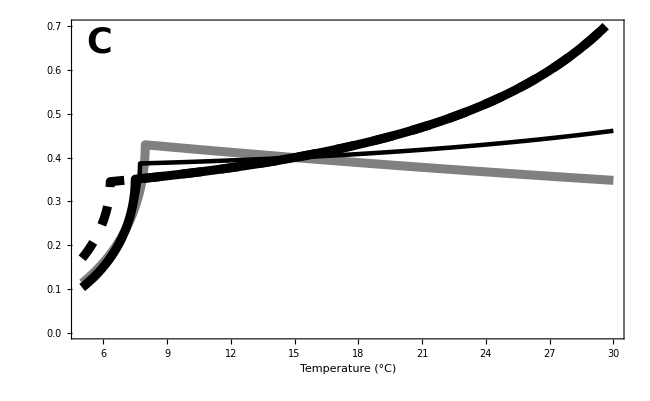

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->{0,0.7}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,0.7}],
PlotRange->{0,0.7},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style[(*"Stability"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Stability (-λ)",LabelSize],Scaled@ylabpos],90 Degree]
}
]

Export[imagedir<>"StabilityType1.pdf",%];
```

## Figure 1 (D,E,F) [ES>EB, type-II]

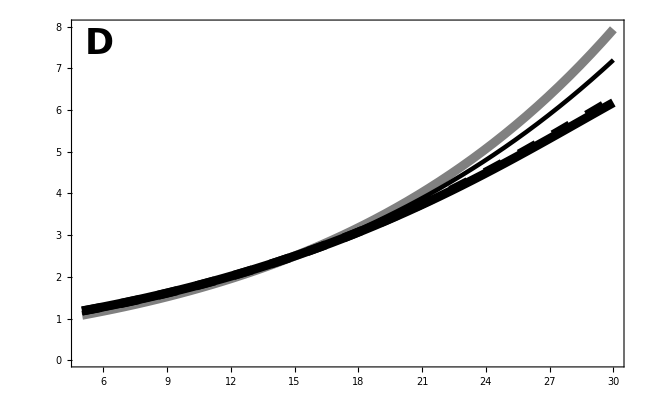

```mathematica
(*Legended[*)
Show[
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red},Axes->False],*)
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01],Dashing[Large]}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Lighter[Blue],Thickness[0.01]}],*)
PlotRange->{0,8},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"B_CR"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
](*,
Placed[
LineLegend[{
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.25]],
Directive[Gray,Thickness[0.25]],
Directive[Gray,Dashing[Medium],Thickness[0.25]]
},
{
Style["β_R=β_C=0.00, type-II",LabelSize],
Style["β_R=β_C=0.02, type-II",LabelSize],
Style["β_R=β_C/2=0.02, type-II",LabelSize],
Style["β_R=β_C=0.04, type-II",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.7}
] 
]*)

Export[imagedir<>"BCRType2.pdf",%];
```

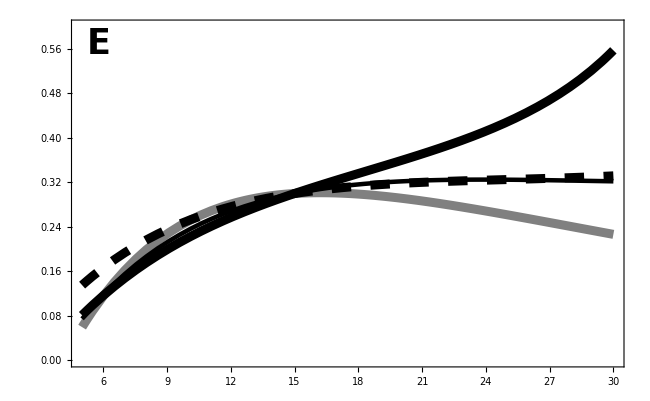

```mathematica
Show[
(*Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False,PlotRange->{0,All}],*)
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"Ĉ:R̂"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"CtoRType2.pdf",%];
```

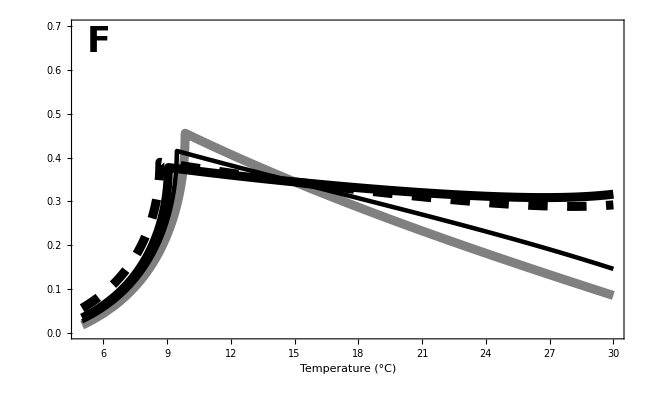

```mathematica
Show[(*Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],*)
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
PlotRange->{0,0.7},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style[(*"Stability"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos]
},
PlotRange->All
]

Export[imagedir<>"StabilityType2.pdf",%];
```

## Figure S1 (A,B,C) [ES<EB, type-I]

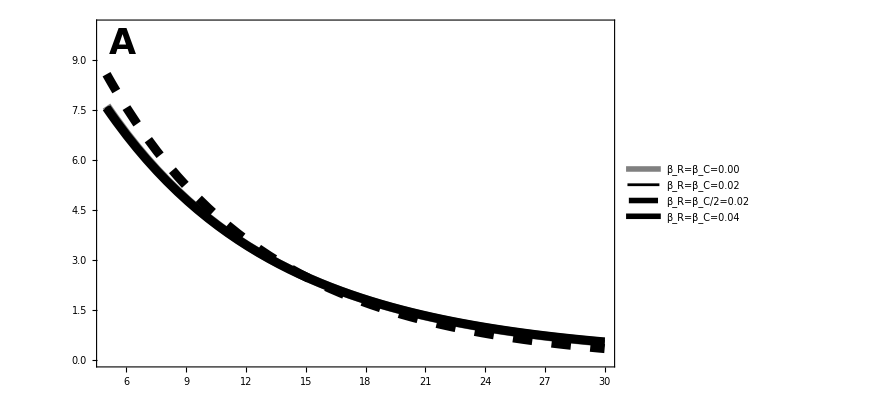

```mathematica
Legended[
Show[
(*Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[
BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray},Axes->False,PlotRangePadding->None],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.005],Black},PlotRangePadding->None],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]},PlotRangePadding->None],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black},PlotRangePadding->None],
PlotRange->{0,10},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"B_CR"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.25]],
Directive[Black,Thickness[0.1]],
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.35]]
},
{
Style["β_R=β_C=0.00",LabelSize],
Style["β_R=β_C=0.02",LabelSize],
Style["β_R=β_C/2=0.02",LabelSize],
Style["β_R=β_C=0.04",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.65,0.7}
] 
]

(*Export[imagedir<>"BCRType1.pdf",%];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

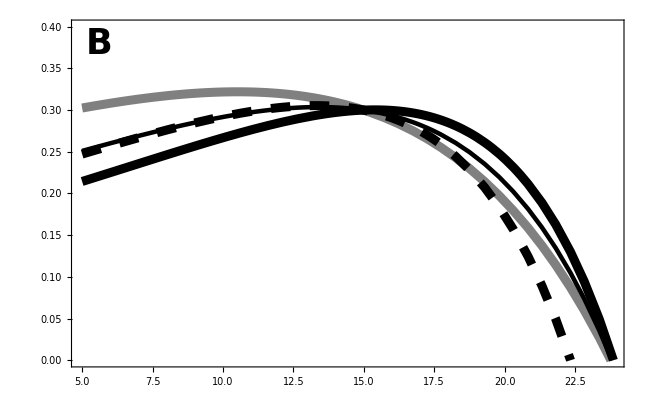

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
PlotRange->{0,0.4},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"Ĉ:R̂"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Ĉ:R̂",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"CtoRType1.pdf",%];*)
```

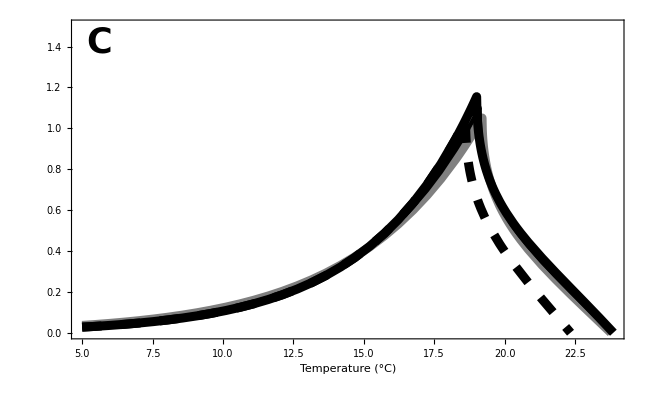

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,1.5},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style[(*"Stability"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Stability",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"StabilityType1.pdf",%];*)
```

### Paradox of enrichment in reverse (why stability increases and then declines)

We see the sudden drop in stability around 19 degrees C because this is where population cycles end (ie, where the eigenvalues become real). Below 19C the carrying capacity K is relatively large and there are population cycles. Decreasing K in this region increases stability (paradox of enrichment in reverse).  Above 19C K is relatively small and there are no population cylces. Decreasing K in this region decreases stability.

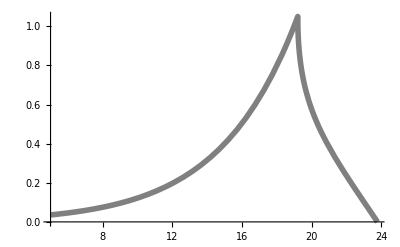

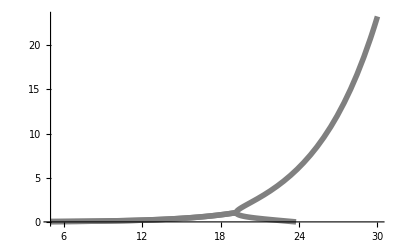

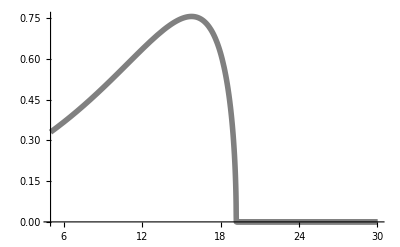

```mathematica
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}]

Plot[-Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}]

Plot[Im[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}]
```

## Figure S1 (D,E,F) [ES<EB, type-II]

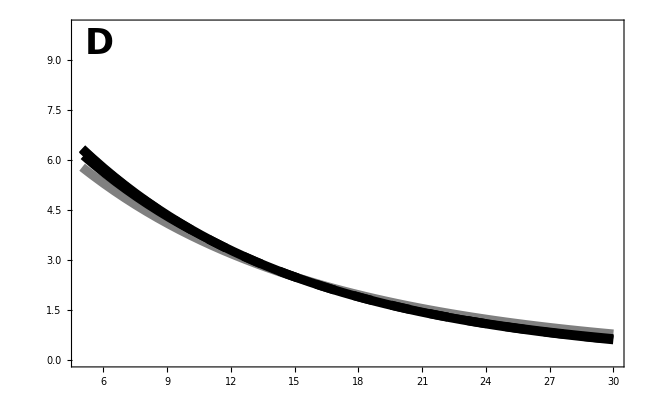

```mathematica
(*Legended[*)
Show[
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red},Axes->False],*)
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01],Dashing[Large]}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Lighter[Blue],Thickness[0.01]}],*)
PlotRange->{0,10},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"B_CR"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
](*,
Placed[
LineLegend[{
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.25]],
Directive[Gray,Thickness[0.25]],
Directive[Gray,Dashing[Medium],Thickness[0.25]]
},
{
Style["β_R=β_C=0.00, type-II",LabelSize],
Style["β_R=β_C=0.02, type-II",LabelSize],
Style["β_R=β_C/2=0.02, type-II",LabelSize],
Style["β_R=β_C=0.04, type-II",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.7}
] 
]*)

(*Export[imagedir<>"BCRType2.pdf",%];*)
```

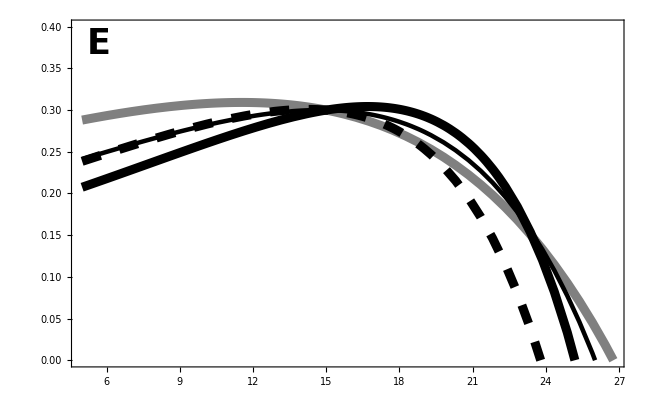

```mathematica
Show[
(*Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False,PlotRange->{0,All}],*)
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.4},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"Ĉ:R̂"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"CtoRType2.pdf",%];*)
```

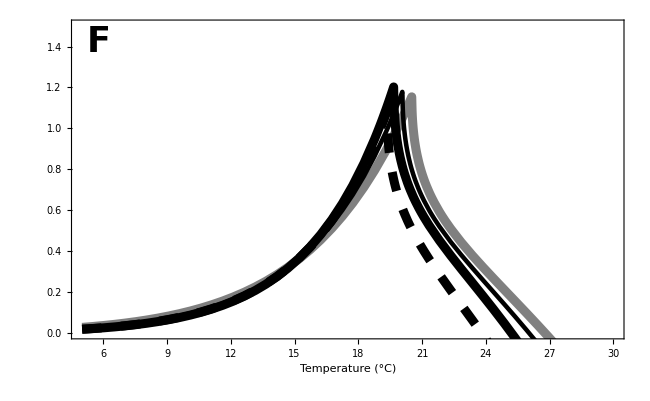

```mathematica
Show[(*Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],*)
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
PlotRange->{0,1.5},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style[(*"Stability"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos]
},
PlotRange->All
]

(*Export[imagedir<>"StabilityType2.pdf",%];*)
```

## Figure S2 (A,B,C) [ES=EB, type-I]

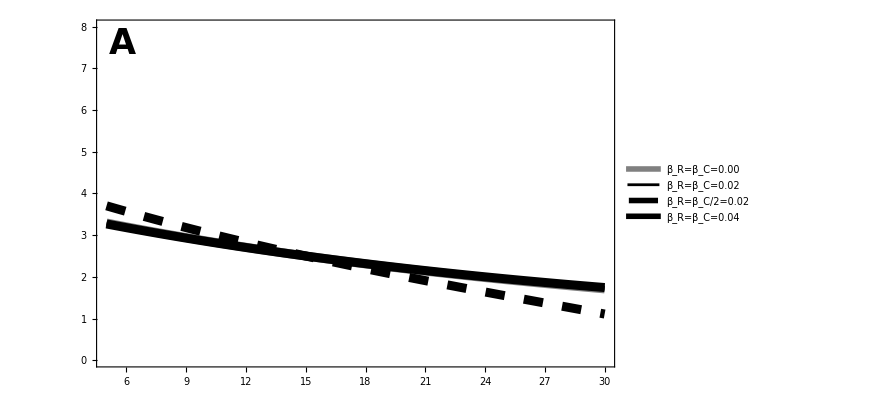

```mathematica
Legended[
Show[
(*Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[
BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray},Axes->False,PlotRangePadding->None],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.005],Black},PlotRangePadding->None],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]},PlotRangePadding->None],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black},PlotRangePadding->None],
PlotRange->{0,8},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"B_CR"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.25]],
Directive[Black,Thickness[0.1]],
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.35]]
},
{
Style["β_R=β_C=0.00",LabelSize],
Style["β_R=β_C=0.02",LabelSize],
Style["β_R=β_C/2=0.02",LabelSize],
Style["β_R=β_C=0.04",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.65,0.7}
] 
]

(*Export[imagedir<>"BCRType1.pdf",%];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

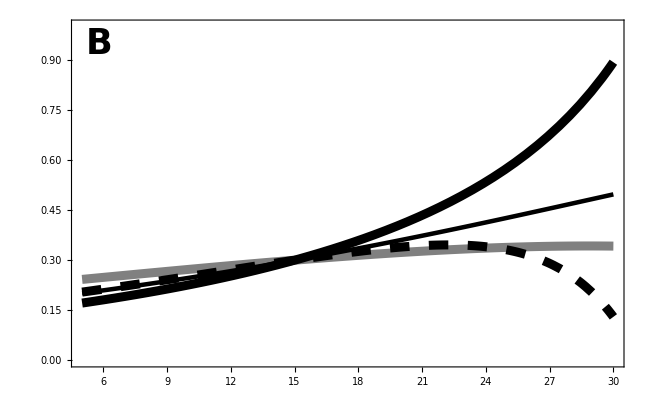

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
PlotRange->{0,1},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"Ĉ:R̂"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Ĉ:R̂",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"CtoRType1.pdf",%];*)
```

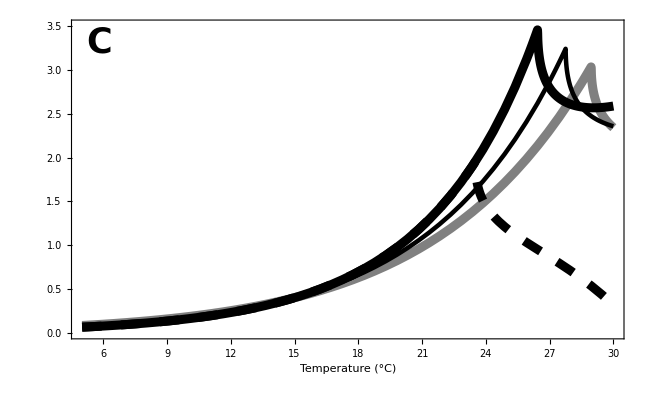

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.04/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,3.5},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style[(*"Stability"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
PlotRangeClipping->False,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Stability",LabelSize],Scaled@ylabpos],90 Degree]
}
]

(*Export[imagedir<>"StabilityType1.pdf",%];*)
```

## Figure S2 (D,E,F) [ES=EB, type-II]

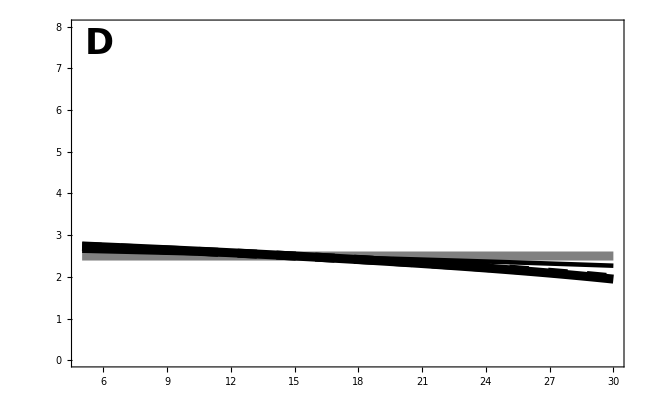

```mathematica
(*Legended[*)
Show[
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Gray,Thickness[0.01]}],*)
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red},Axes->False],*)
(*Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],*)
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Gray,Thickness[0.01]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.005]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},Axes->False],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
(*Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01],Dashing[Large]}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Lighter[Blue],Thickness[0.01]}],*)
PlotRange->{0,8},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"B_CR"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
](*,
Placed[
LineLegend[{
Directive[Black,Dashing[Medium],Thickness[0.25]],
Directive[Black,Thickness[0.25]],
Directive[Gray,Thickness[0.25]],
Directive[Gray,Dashing[Medium],Thickness[0.25]]
},
{
Style["β_R=β_C=0.00, type-II",LabelSize],
Style["β_R=β_C=0.02, type-II",LabelSize],
Style["β_R=β_C/2=0.02, type-II",LabelSize],
Style["β_R=β_C=0.04, type-II",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.7}
] 
]*)

(*Export[imagedir<>"BCRType2.pdf",%];*)
```

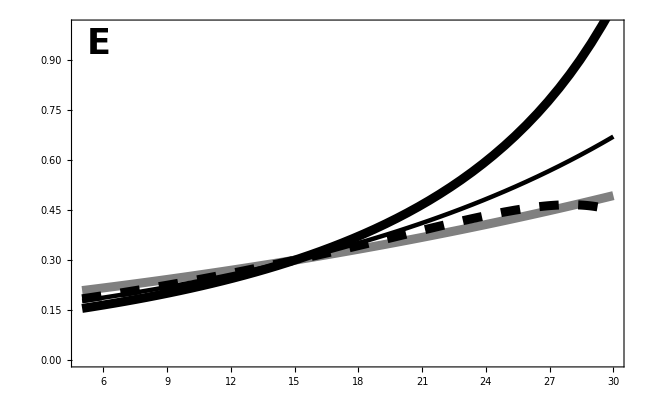

```mathematica
Show[
(*Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False,PlotRange->{0,All}],*)
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1,{t,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,1},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style[(*"Ĉ:R̂"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos]
}
]

(*Export[imagedir<>"CtoRType2.pdf",%];*)
```

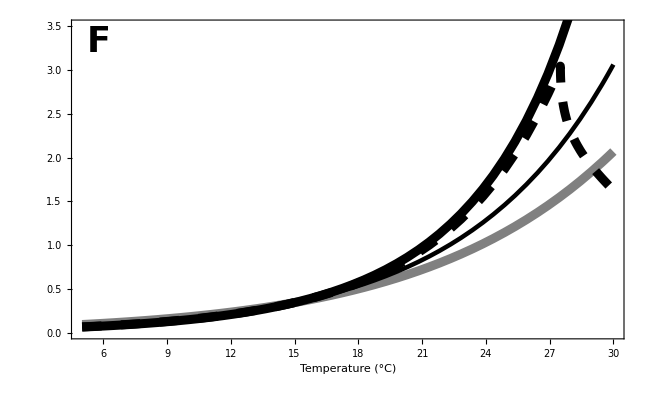

```mathematica
Show[(*Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],*)
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.00/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Gray,Thickness[0.01]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Thickness[0.005]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[R]->0.02/.β[C]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Dashing[Large],Thickness[0.01]},PlotRange->All],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.04/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
PlotRange->{0,3.5},
Frame->True, 
FrameLabel->{Style["Temperature (°C)",LabelSize],Style[(*"Stability"*)"",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos]
},
PlotRange->All
]

(*Export[imagedir<>"StabilityType2.pdf",%];*)
```